```mathematica
SetDirectory["/Users/mobileryan/Dropbox/Triplet-DNP/Programs"]
```

/Users/mobileryan/Dropbox/Triplet-DNP/Programs

```mathematica
preData=Import["./test.dat","Data" ];
{dimX, dump}=Dimensions[preData[[2;;-1]]]
YData=preData[[1]];
dimY=Length[YData]
Data[j_]:=Table[{preData[[i,1]],preData[[i,j+1]]},{i,2,dimX}]
```

{1002,351}

350

```mathematica
ArrayPlot[preData[[2;;-1]],ColorFunction->"Rainbow",AspectRatio->1]
```

-Graphics-

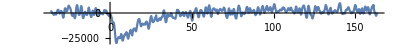

{B-Field,3.52,-4.6,mean,727.391,sd,2941.18}

```mathematica
data=Data[180];
ListPlot[data, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full] 
{"B-Field",YData[[180]],data[[160,1]],"mean",noiseLevel=Mean[data[[1;;160,2]]], "sd",sd=StandardDeviation[data[[1;;160,2]]]}
```

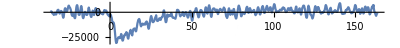

{-4.6,mean,7.04858×10^-13,sd,2941.18}

```mathematica
data=Table[{data[[i,1]],data[[i,2]]-noiseLevel},{i,1,Length[data]}];
ListPlot[data, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full] 
{data[[160,1]],"mean",Mean[data[[1;;160,2]]], "sd",StandardDeviation[data[[1;;160,2]]]}
```

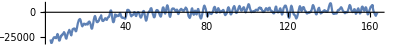

```mathematica
g1=ListPlot[data[[200;;-1]], Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full]
```

```mathematica
Func[t_,a_,Ta_]:=a Exp[-t/Ta]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 1873.36 | 669.668 | 2.79745 | 0.00527475
Ta | -1.59464×10^6 | 7.27898×10^9 | -0.000219074 | 0.999825
b | -38849. | 847.423 | -45.8437 | 8.79054×10^-226
Tb | 19.331 | 0.968584 | 19.958 | 3.35919×10^-72

| DF | SS | MS
Model | 4 | 4.27974×10^10 | 1.06994×10^10
Error | 798 | 6.42478×10^9 | 8.05111×10^6
Uncorrected Total | 802 | 4.92222×10^10 | 
Corrected Total | 801 | 4.57765×10^10 |

{mean,1006.33,sd,2932.92}

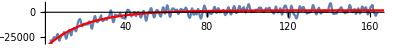

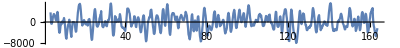

```mathematica
nlm=NonlinearModelFit[data[[200;;-1]],{ Func[t, a, Ta]+Func[t,b,Tb],Ta<Tb , a>0, 0>b}, {a, Ta,b,Tb}, t];
nlm["ParameterTable"]
nlm["ANOVATable"] 
{"mean",Mean[diff[[1;;-1,2]]], "sd",StandardDeviation[diff[[1;;-1,2]]]}
Show[
g1,
Plot[nlm[t],{t,0,200}, PlotRange->All, PlotStyle->Red]
]
diff=Table[{data[[i,1]],data[[i,2]]-nlm[data[[i,1]]]},{i,200,Length[data]}];
ListPlot[diff, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full]
```